# μLang — Computationally Generating a Morphologically Average Conlang Lexicon from Multilingual Translations

Constructed languages, or conlangs, are languages that were artificially created instead of being naturally evolved over several generations. A crucial part of every conlang is the lexicon — the vocabulary. While most conlang lexicons are generated manually or through the help of random combination algorithms, I introduce several algorithms and metrics for computationally generating a quantitatively “average” lexicon, that is, generating new words that may have similar features, spelling, or pronunciation compared to several translations of the same word in different languages. In the end, I present μLang, a conlang lexicon using computationally generated “average” words.

...have...from translations of the same word in several languages.

## Introduction

A conlang’s lexicon can offer crucial information about the purpose and intended speakers of the conlang. The conlang Esperanto was created in 1887, aiming to create a “universal” language that could be learned and spoken by anyone with relative ease. However, Esperanto’s lexicon was heavily biased towards Romance and Germanic languages, undermining its original purpose of being universal. This research uses genetic algorithms, neural networks, and other approaches to attempt to quantify universality and generate a lexicon that is the optimal “average” of the world languages.

“..., created in 1887,...”  Otherwise, “aiming” is a dangling participle.

Your choice, but “research” does not seem to describe what you have done in my mind. Perhaps investigation or exploration or project? If you like research, stick with it.

## Initial Setup

In order to derive average words, I needed a large corpus of multilingual words. I used the built-in database of languages in the Wolfram Language. Because not all languages use the Latin alphabet, I transliterated all language into the Latin alphabet. Additionally, I deleted any duplicates that may have biased the training data.

Get the top 100 most spoken languages:

```mathematica
languages=EntityClass["Language",{"TotalSpeakers"->TakeLargest[100]}]//EntityList;
Iconize[languages, "List of languages"]
```

Get raw translations of our keyWord to the determined languages:

```mathematica
keyWord = "sun";
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation[keyWord, languages]];
rawTranslations//Short
```

{Chinese→太陽,English→sun,Mandarin Chinese→太陽,Hindi→सूर्य,Arabic→شَمس,Spanish→sol,French→soleil,Standard Arabic→NotAvailable,Bengali→সূর্য্য,Russian→солнце,Portuguese→sol,«78»,Afrikaans→son,Southern Pashto→NotAvailable,Chhattisgarhi→NotAvailable,Rajasthani→NotAvailable,Cebuano→adlaw,Mesopotamian Arabic→NotAvailable,Nigerian Fulfulde→NotAvailable,Assamese→সূর্য্য,Northeastern Thai→NotAvailable,Zhuang→NotAvailable,Northern Kurdish→NotAvailable}

Standardize all translated words — Transliterate to the Roman alphabet for easier string manipulation, ensure all words are lowercase, and remove translations that are not available.

```mathematica
translatedList=DeleteCases[DeleteDuplicates[ToLowerCase[Select[Transliterate[Values[rawTranslations]],StringMatchQ[#,CharacterRange["A","z"]..]&]]], "notavailable"]
```

{sun,surya,shams,sol,soleil,suryya,solnce,matahari,swrj,sonne,ri,jua,nuryudu,gunes,katiravan,taeyang,rana,srengenge,sole,phraxathity,suraja,slonce,suran,taiyang,sonce,panonpoe,anwu,ilanga,aftab,araw,soare,zon,qorrax,son,adlaw}

There is a function DeleteMissing. You might use that instead of DeleteCases.

## Most Common Letter

The first thing I thought of was to join the most frequent characters together. I counted the most frequent letter at every index, found the average length of the original words, and concatenated the most common letters together to form a new string equal to the length of the average length.

Split each word into a List of characters:

```mathematica
charLists = Characters /@ translatedList;
charLists//Short
```

{{s,u,n},{s,u,r,y,a},{s,h,a,m,s},{s,o,l},{s,o,l,e,i,l},{s,u,r,y,y,a},«23»,{a,r,a,w},{s,o,a,r,e},{z,o,n},{q,o,r,r,a,x},{s,o,n},{a,d,l,a,w}}

Normalize the lengths of the words through padding and truncation using the average length:

```mathematica
avgLen=Round[Mean[Length/@charLists]];

augmentedLists=
Map[
Function[chars,
If[Length[chars]>avgLen,
Take[chars,avgLen],
PadRight[chars,avgLen,"-"]
]
],charLists];

augmentedLists//Short
```

{{s,u,n,-,-},{s,u,r,y,a},{s,h,a,m,s},{s,o,l,-,-},{s,o,l,e,i},{s,u,r,y,y},«24»,{s,o,a,r,e},{z,o,n,-,-},{q,o,r,r,a},{s,o,n,-,-},{a,d,l,a,w}}

I transpose the list of characters to align all the characters into their corresponding indices.

Find the most frequent character at each position and generate the average word:

```mathematica
transposed=Transpose[augmentedLists];

mostFreqChar=If[DeleteCases[#,"-"]==={},"-",SortBy[Tally@DeleteCases[#,"-"],-Last[#]&]][[1, 1]]&/@transposed;
```

```mathematica
mostFreqCharWord=StringJoin[DeleteCases[mostFreqChar,"-"]];
"Average word generated with the most frequent character at each position: " <> mostFreqCharWord
```

Average word generated with the most frequent character at each position: sonaa

Generate an animation of the most common character at each index and the generation of the word:

```mathematica
animatedFreq=Table[Module[{partialTransposed,partialMostFreq,charCounts,sortedCounts,labels},partialTransposed=Take[transposed,i];
partialMostFreq=Map[If[DeleteCases[#,"-"]==={},"-",First@First@SortBy[Tally@DeleteCases[#,"-"],-Last[#]&]]&,partialTransposed];
charCounts=Tally@DeleteCases[partialTransposed[[-1]],"-"];
sortedCounts=ReverseSortBy[charCounts,Last];
labels=Placed[sortedCounts[[All,1]],Below];
Column[{Style["Position: "<>ToString[i],Bold,16],Style[StringJoin[DeleteCases[partialMostFreq,"-"]],24,Red],BarChart[sortedCounts[[All,2]],ChartLabels->labels,ImageSize->Large,PlotLabel->"Character Frequency at Position "<>ToString[i]]}]],{i,1,Length[transposed]}];

ListAnimate[animatedFreq,AnimationRate->0.5,DefaultDuration->20,ImageSize->Large, SaveDefinitions->True]
```

While this method does work, it may not be optimally average. If there are two characters of equal frequency at a position, there is a chance the suboptimal character is selected. Additionally, this approach doesn’t produce very creative words. It always outputs one very predictable word and there is no variance. To generate words with more variety, I explored more methods.

## Most Common Digram

My second approach was to split each word into digrams (pairs of consecutive letters) and find the most common digram in each position. Then, we can join the most common digrams together. For example, “su” is the first digram in “sun” and “un” is the second digram in “sun.” Joining the two digrams would output “suun.”

Calculate the average syllable count:

```mathematica
syllableCount = Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
```

2

Split each word into digrams and record the position of each digram:

```mathematica
positionedDigrams=Flatten[
Table[
If[
StringLength[word]>=pos+1,
{pos,StringTake[word,{pos,pos+1}]},
Nothing],
{word,translatedList},
{pos,StringLength[word]-1}
],1];
positionedDigrams//Short
```

{{1,su},{2,un},{1,su},{2,ur},{3,ry},{4,ya},{1,sh},{2,ha},{3,am},{4,ms},{1,so},{2,ol},{1,so},{2,ol},«127»,{4,re},{1,zo},{2,on},{1,qo},{2,or},{3,rr},{4,ra},{5,ax},{1,so},{2,on},{1,ad},{2,dl},{3,la},{4,aw}}

Count the frequency of each digram in each position:

```mathematica
groupedByPosition=GroupBy[positionedDigrams,First->Last];
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
countsByPosition//First
```

<|su→5,sh→1,so→8,ma→1,sw→1,ri→1,ju→1,nu→1,gu→1,ka→1,ta→2,ra→1,sr→1,ph→1,sl→1,pa→1,an→1,il→1,af→1,ar→1,zo→1,qo→1,ad→1|>

Get the most frequent digram in each position:

```mathematica
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[1]],{pos,Sort@Keys[countsByPosition]}]
```

{{so},{ur},{ry},{ya},{ce},{ng},{ri},{an},{it},{ty}}

Generate new words by randomly combining the most frequent digrams:

```mathematica
generateWord[]:=Module[{numSyllables,selectedLists,syllables},
numSyllables:=RandomInteger[{Max[1, syllableCount-2], Min[Length[topDigramsByPosition], syllableCount+2]}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]
]
```

Suggest a few possible words using random combinations of the most frequency digrams:

```mathematica
mostDigramGenerated=DeleteDuplicates[Table[generateWord[],{7}]];
"Possible average words generated through random digram concatenation: " TableForm[mostDigramGenerated]
```

Possible average words generated through random digram concatenation:  sourry
sourryya

This method isn’t ideal either. While it occasionally produces pronounceable words, it relies too heavily on common digrams and uses a very basic substitution approach. Since some digrams end with the same letter others begin with, the result is often awkward combinations, like doubled vowels or consonants, making the words harder to read and pronounce. Both of the previous methods suffer from the same issue: they depend too rigidly on character frequency.

## Genetic Evolution

Another approach is to treat the most average word as an optimal evolutionary trait. Imagine the original list of translated words as a starting population, all trying to evolve closer to this ideal average word. Using a genetic algorithm, we can simulate this evolution by selecting the most optimal words in each generation and creating new, unique words that are similar in morphology to the multilingual wordlist but still contains minor mutations that encourage further evolution

In each generation, I select the top 50% of the most fit words to be parents. These parents undergo a modified two-point crossover, which allows the child words to be more flexible with their length. Additionally, each word has a 20% chance to mutate, meaning a random character in the word is changed. This process repeats generation after generation, gradually evolving the population toward the optimal trait.

It appears that you mean orthography when you say morphology. Look up both and see what you think. This is not the only place you use this term.

Define important variables. populationSize is the size of the population each generation and mutationRate:

```mathematica
Clear[populationSize, generations, mutationRate, topDigramsByPosition, fitnessFunction, population, randomString, allBest];
populationSize = 100;
generations = 50;
mutationRate = 0.2;
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}]
allBest = {};
words = translatedList;
charSet = Flatten[topDigramsByPosition];
maxLength = Round[Mean[StringLength/@ words]];
allPopulations = {};
avgFitnessPerGen = {};
```

{{so,su,ta,sh,ma},{ur,ol,on,un,at},{ry,ra,le,ta,am},{ya,nc,ng,ms,ei},{ce,an,il,ya,ha},{ng,ar,du,av,en},{ri,va,ng,th,oe},{an,ge,hi},{it},{ty}}

To quantify how close a given word is to an “optimally average” word, I defined a fitness function where higher fitness scores reflect a word closer to the average. The measure of “closeness” is based on a weighted sum of two factors: the mean Levenshtein distance between the candidate word and all words in a multilingual wordlist, and the average phonetic distance between the candidate word and the same wordlist.

To measure the phonetic distance, I used the Soundex to convert the transliterated words into generalized phonetic markers. Word with similar phonetics will be considered more similar or even equal. For example, “back” and “pack” will be closer than “back” and “rack” because the /b/ and /p/ sounds have the same place of articulation.

```mathematica
phoneticDifference["back", "pack"]
```

phoneticDifference[back,pack]

```mathematica
phoneticDifference["back", "rack"]
```

phoneticDifference[back,rack]

Define the fitness function:

```mathematica
phoneticDifference[word1_String,word2_String]:=Module[{soundex1,soundex2},
soundex1=ResourceFunction["Soundex"][word1];
soundex2=ResourceFunction["Soundex"][word2];
If[soundex1===soundex2,0,EditDistance[soundex1,soundex2]]];

fitnessFunction[candidate_String]:=Module[{maxEditDistance,maxPhoneticDistance,editScore,phoneticScore},
maxEditDistance=Max[EditDistance[candidate,#]&/@words];
maxPhoneticDistance=Max[phoneticDifference[candidate,#]&/@words];
editScore=If[maxEditDistance>0,1-N[Mean[EditDistance[candidate,#]&/@words]/maxEditDistance],1];
phoneticScore=If[maxPhoneticDistance>0,1-N[Mean[phoneticDifference[candidate,#]&/@words]/maxPhoneticDistance],1];
0.5*editScore+0.5*phoneticScore
];
```

Note the fitness of a word similar to possible keyWord translations is significantly greater than a completely unrelated string:

```mathematica
fitnessFunction[WordTranslation[keyWord, "Spanish"][[1]]]
```

0.53539

```mathematica
fitnessFunction["random string"]
```

0.127198

My initial population will be a list of randomly combined digrams. This allows the population to start off reasonably similar to the multilingual wordlist but also allows diversity for future recombination.

Create our original population by randomly combining digrams:

```mathematica
randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{syllableCount,syllableCount+2}]];
population=Table[randomString[],{populationSize}];
population
```

{raunngan,anle,msonam,shunnc,antaon,leanavya,angethry,atoety,thur,eihancei,hian,dutyan,dudu,eidums,sovaon,ilgehi,ceya,yasu,unyangan,shtaavam,nghi,rang,ngolsuty,ngngngei,raeilera,lege,olri,enunansu,amcetang,ryilsu,amavma,ngng,shhiamat,yayams,anarhams,raun,vamaol,ilge,ngva,ngsh,rasuonat,shavarso,sham,ilitha,ceunmsan,soansh,tara,ngarva,avrysu,shngleav,oltyit,taeivava,olatsota,enon,unriya,taolta,untyya,taoeon,enitso,ryarma,anra,raaronth,vavang,maaran,gevaamry,arms,anamngty,suge,ryduyadu,geit,olhang,tash,itonta,leanri,unngsh,vara,thvasu,atonry,lehice,itshraat,raya,hiduthit,eimaya,unduya,msso,yaunryol,anavnc,tyhing,sungng,eiilitya,sududu,tadu,gerioe,thilonur,vavaat,anan,ilil,aranurce,ryatavam,eioece}

With everything set up, I can simulate evolution. I used a modified two-point crossover algorithm that allowed both parent words to vary in length. I choose two random points within the shorter parent as crossover points.  Then, the head and tail of the first parent is combined with the center of the second parent.

Implementation of two-point crossover:

```mathematica
lengthVaryTwoPointCrossover[p1_,p2_]:=Module[{len1,len2,minLen,pt1,pt2,c1,c2,child},
len1=StringLength[p1];
len2=StringLength[p2];
minLen=Min[len1,len2];
{pt1,pt2}=Sort@RandomSample[Range[minLen],2];
c1=Characters[p1];
c2=Characters[p2];
child=Join[Take[c1,pt1-1],Take[c2,{pt1,pt2}],Drop[c1,pt2]];
If[
Length[child]>
maxLength,
child=Take[child,maxLength]
];
StringJoin[child]];
```

Implementation of string mutation:

```mathematica
mutate[str_]:=StringJoin@
Table[
If[RandomReal[]<mutationRate,
RandomChoice[charSet],
c
],
{c,Characters[str]}
];
```

I record the best/”most fit” word each generation:

```mathematica
allBest=Table[fitnesses=fitnessFunction/@population;
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
avgF=N[Mean[fitnesses]];
AppendTo[avgFitnessPerGen,avgF];
AppendTo[allPopulations,population];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
population=Table[mutate@lengthVaryTwoPointCrossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];
bestCandidate,{gen,1,generations}
];

AppendTo[allPopulations,population];
```

The best performing strings in each generation:

```mathematica
allBest
```

{suge,sums,soen,sonaa,senh,senh,syyan,sour,sounn,syne,sayn,syono,saona,suian,suane,sunne,syoon,soyno,suono,suono,suenc,suonu,sonae,sonae,soone,soone,soeyn,soane,soure,sounn,sonye,sunye,sanma,suene,sanne,sonau,sonne,synne,soone,syone,sonne,seonn,ssune,sonya,syane,sanua,soane,seune,sonoe,soane}

Log the most fit string:

```mathematica
bestWordGeneticPool=First@MaximalBy[allBest,fitnessFunction];
"Best word found: "  <> ToString[bestWordGeneticPool]
"Fitness of best word: "<>ToString[fitnessFunction[bestWordGeneticPool]]
```

Best word found: syne

Fitness of best word: 0.563312

Plot the average fitness of every population of each generation over time:

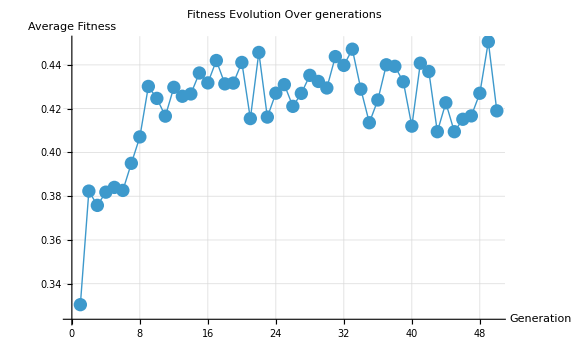

```mathematica
ListLinePlot[avgFitnessPerGen,PlotRange->All,Mesh->All,PlotStyle->Thick,AxesLabel->{"Generation","Average Fitness"},PlotLabel->"Fitness Evolution Over generations",GridLines->Automatic, ImageSize->Large]
```

Overall, there is a clear trend of increasing fitness throughout the entire evolutionary period. There is a particularly rapid increase during the first 15 generations as the population quickly adapts to the multilingual wordlist. This shows the entire population is evolving towards both morphological and phonetic traits in the word list.

Plot the fitness of the best candidate in each generation over time:

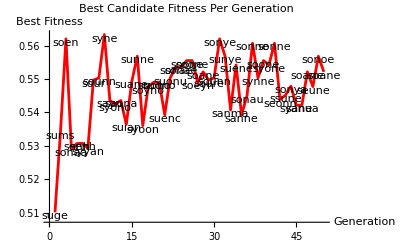

```mathematica
bestPerGenPlot=ListPlot[Table[{gen,fitnessFunction[allBest[[gen]]]},{gen,Length[allBest]}],PlotStyle->{Red,PointSize[Medium]},Joined->True,PlotRange->All,AxesLabel->{"Generation","Best Fitness"},Epilog->Table[Text[Style[allBest[[gen]],Medium],{gen,fitnessFunction[allBest[[gen]]]}+{0,-0.0012}],{gen,Length[allBest]}],PlotLabel->"Best Candidate Fitness Per Generation",ImageSize->Full]
```

This shows a very weak increasing trend in the fitness of the most fit words in every generation. Both graphs above show clear improvement in the fitness of the population and best word, demonstrating that my genetic algorithm is effective.

## String Optimization

Building the μLang lexicon can also be viewed as an optimization problem. Given a random string, I can iteratively change its characters to increase its fitness and, at some point, achieve an optimal average word. The goal is to evolve a string that minimizes the average edit distance to all multilingual words. In each generation, I identify the word with the highest edit distance from the current string and modify a single character in the string to match a character from that word. Over time, this process converges on an optimal average word.

Set up basic variables and helper functions to get differing indices between words and calculate positions for the words to occupy on the animation.

```mathematica
Clear[baseWord, testList, padChar, baseWordStates, targetWords,generations];
baseWord=StringJoin@RandomChoice[CharacterRange["a", "z"], 5];
startingWord = baseWord;
testList=translatedList
padChar="_";
baseWordStates={baseWord};
targetWords={};
generations=1000;
averageLength=Round[Mean[StringLength /@ testList]];

getAllChars[wordList_]:=Module[{maxLen,paddedWords,allChars},
maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
allChars=Union[Flatten[Characters/@paddedWords]];
allChars
];

pad[w1_,w2_]:=Module[{maxLen,p1,p2},
maxLen=Max[StringLength[w1],StringLength[w2]];
{StringPadRight[w1,maxLen,padChar],StringPadRight[w2,maxLen,padChar]}
];

mostDifferentWord[base_,list_]:=Module[{diffs},diffs=Table[{word,EditDistance[base,word]},{word,list}];
First@MaximalBy[diffs,Last]];

findDifferingIndices[str1_,str2_]:=Module[{minLen,diffs},minLen=Min[StringLength[str1],StringLength[str2]];
diffs=Select[Range[minLen],StringTake[str1,{#}]=!=StringTake[str2,{#}]&];
diffs]

layoutTestWords[baseWord_, testList_] := 
  Module[{angles, positions}, 
   angles = Subdivide[0, 2*Pi, Length[testList]][[1 ;; -2]];
   positions = Table[
     With[{dist = EditDistance[baseWord, testList[[i]]]},
      {testList[[i]], 
       Cos[angles[[i]]]*dist, 
       Sin[angles[[i]]]*dist}
      ], {i, 1, Length[testList]}];
   positions];
```

{sun,surya,shams,sol,soleil,suryya,solnce,matahari,swrj,sonne,ri,jua,nuryudu,gunes,katiravan,taeyang,rana,srengenge,sole,phraxathity,suraja,slonce,suran,taiyang,sonce,panonpoe,anwu,ilanga,aftab,araw,soare,zon,qorrax,son,adlaw}

I assign a weight to each character based on its frequency. This way, I encourage evolving towards more frequent characters at any position.

Calculate character frequencies for each position:

```mathematica
calculateCharFrequencies[wordList_]:=Module[{maxLen,paddedWords,freqTables},
maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
freqTables=Table[Counts[StringTake[#,{pos}]&/@paddedWords],{pos,1,maxLen}];
freqTables
]
```

Normalize frequencies to a decimal number between 0 and 1:

```mathematica
normalizeFrequencies[freqTable_]:=Module[{nonZeroEntries,total},
nonZeroEntries=Select[freqTable,#>0&];
total=Total[Values[nonZeroEntries]];
If[
total==0,
freqTable,
Association[#->If[freqTable[#]>0,N[freqTable[#]/total],0]&/@Keys[freqTable]]
]
]
```

Calculate weighted character frequencies:

```mathematica
allPossibleChars=getAllChars[testList];
rawFrequencies=calculateCharFrequencies[testList];

charFreqWeights=Map[normalizeFrequencies[AssociationThread[allPossibleChars,Lookup[#,allPossibleChars,0]]]&,rawFrequencies];
```

Decide the character to evolve into based on the frequency weightings:

```mathematica
weightedRandomTarget[base_,list_]:=Module[{diffs,total,weights},
diffs=Table[{word,EditDistance[base,word]},{word,list}];
total=Total[diffs[[All,2]]];
If[total==0,

RandomChoice[list],
weights=(diffs[[All,2]]^3)/Total[diffs[[All,2]]^3];
RandomChoice[weights->diffs[[All,1]]]]
];
```

Mutate a character at randomly 5% of the time:

```mathematica
randomMutation[word_,rate_:0.05]:=Module[{chars,mutated},chars=Characters[word];
mutated=Map[If[RandomReal[]<rate,RandomChoice[CharacterRange["a","z"]~Join~{padChar}],#]&,chars];
StringJoin[mutated]];
```

Evolve towards the decided character:

```mathematica
evolveTowardWeighted[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i,targetChar,baseChar,weight},{basePadded,targetPadded}=pad[base,target];
diffIndices=findDifferingIndices[basePadded,targetPadded];
If[diffIndices==={},basePadded,
i=RandomChoice[diffIndices];
targetChar=StringTake[targetPadded,{i,i}];
baseChar=StringTake[basePadded,{i,i}];
weight=
If[
i<=Length[charFreqWeights],
chars=Keys[charFreqWeights[[i]]];
weights = Values[charFreqWeights[[i]]];
choice = RandomChoice[weights->chars];
StringReplacePart[basePadded, choice, {i, i}], basePadded]]];
```

Simulate hundreds of generations:

```mathematica
baseWordStates={baseWord};
targetWords={};
bestWord=baseWord;
bestDistance=Mean[EditDistance[baseWord,#]&/@testList];
evolutionStep[{currentWord_,currentBest_,bestDist_,targetHist_,stateHist_}]:=
Module[{target,newWord,newDist},
target=weightedRandomTarget[currentWord,testList];
newWord=StringReplace[evolveTowardWeighted[currentWord,target],"_"->""];
newDist=Mean[EditDistance[newWord,#]&/@testList
];
If[
newDist<bestDist,
{newWord,newWord,newDist,Append[targetHist,target],Append[stateHist,newWord]},
{newWord,currentBest,bestDist,Append[targetHist,target],Append[stateHist,newWord]}
]
];
initialState={baseWord,baseWord,Mean[EditDistance[baseWord,#]&/@testList],{},{baseWord}};
evolutionResults=NestList[evolutionStep,initialState,generations];
{finalWord,bestWord,bestDistance,targetWords,baseWordStates}=Last[evolutionResults];


testPositions=layoutTestWords[baseWordStates[[1]],testList];
positionDict=Association[#[[1]]->{#[[2]],#[[3]]}&/@testPositions];
```

Generate animation of the string evolution and evolutionary targets over time:

```mathematica
createEvolutionAnimation[]:=Module[{frames,maxFrames,basePos={0,0},targetPos,newX,newY,t=0.25},maxFrames=Length[baseWordStates];
frames=Table[Module[{currentWord,target,bx,by,tx,ty},
currentWord=baseWordStates[[frame]];
If[frame<=Length[targetWords],target=targetWords[[frame]],target=targetWords[[-1]]];
targetPos=positionDict[target];
tx=targetPos[[1]];
ty=targetPos[[2]];
If[frame==1,{bx,by}={0,0},newX=basePos[[1]]+t*(tx-basePos[[1]]);
newY=basePos[[2]]+t*(ty-basePos[[2]]);
basePos={newX,newY};
{bx,by}=basePos;];
Show[Graphics[{Gray,Table[Text[Style[StringReplace[testPositions[[i,1]],"_"->""],FontSize->12],{testPositions[[i,2]],testPositions[[i,3]]}],{i,1,Length[testPositions]}],Red,Thickness[0.003],Line[{{bx,by},{tx,ty}}],Red,Text[Style[StringReplace[currentWord,"_"->""],FontSize->18,Bold],{bx,by}],Red,Text[Style["Target: "<>StringReplace[target,"_"->""],FontSize->12],{0,9.5}],Blue}],PlotRange->{{-10,10},{-10,10}},Axes->False,Frame->False,ImageSize->{400,400}]],{frame,1,maxFrames}];
ListAnimate[frames,AnimationRate->5,AnimationRepetitions->1, SaveDefinitions->True]];

createEvolutionAnimation[]

bestWord=StringReplace[bestWord,"_"->""];
"Best word found: " <>bestWord
"Best average distance: "<>ToString[N[bestDistance]]
```

Best word found: sran

Best average distance: 3.97143

The gray words in the circle are from the word list, while the red string represents the word currently evolving. In each generation, the red line points to the target word the red string is aiming to evolve into. As the red word changes step by step, it gets closer to the target, indicating improved fitness between the two.

This is an interesting animation. Did you come up with it yourself?

Plot the average word distance between the evolving string and multilingual word list over generations:

```mathematica
plotEvolutionProgress[baseWordStates_,testList_]:=Module[{distances,generations},distances=Table[Mean[EditDistance[baseWordStates[[i]],#]&/@testList],{i,1,Length[baseWordStates]}];
generations=Range[0,Length[baseWordStates]-1];
ListLinePlot[MovingAverage[Transpose[{generations,distances}], 5],PlotLabel->"Average Distance to Multilingual Wordlist (lower is better)",AxesLabel->{"Generation","Average Distance"},PlotStyle->{Red,Thick},GridLines->Automatic, AspectRatio->1, ImageSize->{550, 550}]]
```

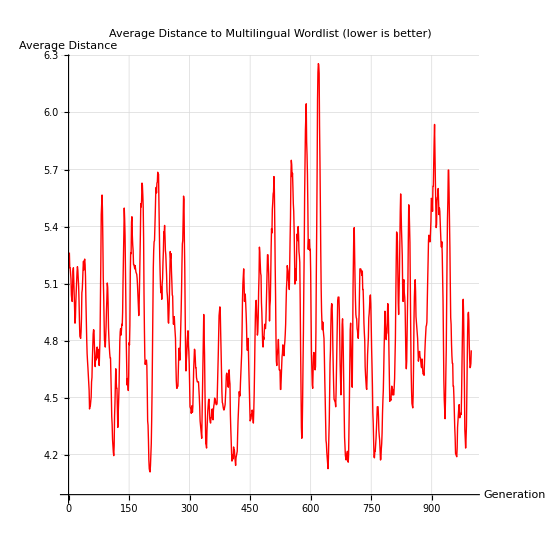

```mathematica
plotEvolutionProgress[baseWordStates, testList]
```

There is not discernable trend in the average distance between the current word

## Generation with Morphological Neural Net Features

A more modern approach may be to take advantage of neural net embeddings. A neural net/deep learning model encodes words in a numeric representation called embeddings or feature vectors. For text, embeddings usually encode semantic meaning, but the . We can ask the neural net to generate new words with similar embedding values as the training set (the original word list), generating new but similar words.

It appears that you have a singular/plural agreement problem unless “embeddings” and “feature vectors” are somehow singular plurals. Perhaps this is intentional.

```mathematica
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
```

NetGraph[…]

Set the vocabulary of characters the neural net can train from and predict to:

```mathematica
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
```

Interesting white space choices.

Replace the default Input port with a NetEncoder that converts input strings to character-level encodings:

```mathematica
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]]
```

NetGraph[…]

It would be cool if you showed an embedding with, say, density plot or just a grid of numbers. It would give the reader a better understanding of what’s going on. Maybe there isn’t time.

Train the neural network on the multilingual dataset:

```mathematica
results = 
 NetTrain[net, <|"Input" -> translatedList|>, All, LossFunction -> "Loss",   MaxTrainingRounds ->500]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1000  rounds:500  time:28s  examples/s:1149
data | ,,  training examples:35  processed examples:32000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:5.92×10^-1  error:23.1%
 | 
 | ]

Extract the prediction layer to act as a character-level generator:

```mathematica
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}]
```

NetChain[<3>]

Now that our model is trained, it can autoregressively generate new strings. At every timestep, the output of the previous timestep is used as the input, allowing the network to predict the most likely letter to follow.

Autoregressively generate new strings:

```mathematica
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,syllableCount,syllableCount+2]];
```

```mathematica
newAvgWords=Sort@Complement[Table[wordz[],15],translatedList]
```

{adla,ilan,kati,qorr,ria}

Concatenate all the possible generated average words from approaches so far:

```mathematica
allPossibleWords = Flatten[Join[{newAvgWords, bestWordGeneticPool, mostDigramGenerated,
     mostFreqCharWord, bestWord}]]
```

{adla,ilan,kati,qorr,ria,syne,sourry,sourryya,sonaa,sran}

Nice job bending a neural net to your bidding.

## Generation with Phonetic Neural Net Features

Does the neural net have features that are phonetic. Reword?

I also apply the same neural net pipeline for multilingual words converted into the International Phonetic Alphabet (IPA).

Initialize the neural network:

```mathematica
netPhon=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
```

NetGraph[…]

Because this network can only accept Roman letters, numerals, and punctuation, I map the IPA symbols to numbers and punctuation symbols .

Set up the mapping association:

```mathematica
symbolMap=<|"θ"->"1","ð"->"2","ʃ"->"3","ʒ"->"4","ɪ"->"5","ɛ"->"6","æ"->"7","ɔ"->"8","ʊ"->"9","ʌ"->"0","ə"->".","ɜ"->",","ŋ"->";","ɡ"->":","ɑ"->"!" ,"ˈ"->"@", "ˌ"->"=", "ɒ"->"*", "ɝ"->"["|>
```

<|θ→1,ð→2,ʃ→3,ʒ→4,ɪ→5,ɛ→6,æ→7,ɔ→8,ʊ→9,ʌ→0,ə→.,ɜ→,,ŋ→;,ɡ→:,ɑ→!,ˈ→@,ˌ→=,ɒ→*,ɝ→[|>

I’ve used a similar scheme before. : )

Convert each multilingual word to its IPA representation and replace the IPA symbols with the symbolMap:

```mathematica
ipaList=ResourceFunction["WordPhoneticSyllabify"][#][[2]]&/@translatedList;
convertedTrainList = StringJoin[Lookup[symbolMap,#,#]&/@Characters[#]]&/@StringReplace[ipaList, "•"->""];
convertedTrainList
```

{suhn,s@9rj.,shamz,sol,sohlahl,s9r@j!,s@o9l.n,m7t.@h!ri,s@wrd4,son,r@a5,joouh,n9r@judu,uhnz,k.@t5r!v.n,t@e5j7;,ranuh,s@r6;6;,sohl,f@r7ks.15ti,s9@r!d4.,sl*ns,s9@r7n,t@a5j7;,s@0ns,p7n.n@po9,7;@wu,i@l!;.,7f@t7b,utput@!r.w,s@8r,zawn,k8@r!,suhn,7d@l8}

```mathematica
vocabularyPhon=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}•"];
```

```mathematica
netPhon=NetReplacePart[netPhon,"Input"->NetEncoder[{"Characters",{vocabularyPhon,{StartOfString,EndOfString}->97}}]]
```

NetGraph[…]

Train the neural network on phonetic data:

```mathematica
resultsPhon = 
 NetTrain[netPhon, <|"Input" -> convertedTrainList|>, All, LossFunction -> "Loss",  MaxTrainingRounds ->500]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1000  rounds:500  time:29s  examples/s:1132
data | ,,  training examples:35  processed examples:32000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:5.27×10^-1  error:18.5%
 | 
 | ]

```mathematica
trainednetPhon=resultsPhon["TrainedNet"];
generatorPhon=NetReplacePart[NetExtract[trainednetPhon,"predict"],{"Input"->NetEncoder[{"Characters",{vocabularyPhon,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabularyPhon,""]}]}]
```

NetChain[<3>]

Autoregressively generate new strings using phonetic symbols:

```mathematica
wordzPhon[]:=With[{obj=NetStateObject[generatorPhon]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,syllableCount,syllableCount+2]];
```

Convert generated strings back into IPA:

```mathematica
newAvgWordsPhonetics=StringJoin[Lookup[Association[Reverse /@ Normal[symbolMap]],#,#]&/@Characters[#]]&/@Sort@Complement[DeleteDuplicates[Table[wordzPhon[],15]], convertedTrainList]
```

{æŋˈw,pænə,ranu,sʊˈr,sʊrˈ,sham,ŋˈwɪ}

## Graphical Interface

To make my algorithms accessible to conlangers and linguists, I designed a GUI for users to experiment with. Given a word, it will display the outputs of all the algorithms discussed in this research. I hope that this GUI will be of use to aspiring conlangers to generate unique but realistic words.

```mathematica
DynamicModule[{keyWord="sun",mostFreqCharWord="",mostDigramGenerated={},syllableCount=0,bestWordGeneticPool="",bestWord="",newAvgWords={}},Panel[Column[{Style["μLang Lexicon Generator",Bold,20],Row[{Style["Enter keyword: ", 15] ,InputField[Dynamic[keyWord],String]}],Button["Generate",Module[{languages,rawTranslations,translatedList,charLists,avgLen,augmentedLists,transposed,mostFreqChar,positionedDigrams,groupedByPosition,countsByPosition,topDigramsByPosition,generateWord,populationSize,generations,mutationRate,fitnessFunction,population,randomString,allBest,words,charSet,maxLength,allPopulations,avgFitnessPerGen,phoneticDifference,bestCandidate,fitnesses,parents,baseWord,testList,padChar,baseWordStates,targetWords,GENERATIONS,averageLength,allPossibleChars,rawFrequencies,charFreqWeights,initialState,evolutionResults,finalWord,bestDistance,testPositions,positionDict,net,vocabulary,results,trainednet,generator,wordz},languages=EntityClass["Language",{"TotalSpeakers"->TakeLargest[100]}]//EntityList;
rawTranslations=KeyValueMap[#1->First[#2]&,WordTranslation[keyWord,languages]];
translatedList=DeleteCases[DeleteDuplicates[ToLowerCase[Select[Transliterate[Values[rawTranslations]],StringMatchQ[#,CharacterRange["A","z"]..]&]]],"notavailable"];


charLists=Characters/@translatedList;
avgLen=Round[Mean[Length/@charLists]];
augmentedLists=Map[Function[chars,If[Length[chars]>avgLen,Take[chars,avgLen],PadRight[chars,avgLen,"-"]]],charLists];
transposed=Transpose[augmentedLists];
mostFreqChar=Map[If[DeleteCases[#,"-"]==={},"-",First@First@SortBy[Tally@DeleteCases[#,"-"],-Last[#]&]]&,transposed];
mostFreqCharWord=StringJoin[DeleteCases[mostFreqChar,"-"]];
syllableCount=Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]];


positionedDigrams=Flatten[Table[If[StringLength[word]>=pos+1,{pos,StringTake[word,{pos,pos+1}]},Nothing],{word,translatedList},{pos,StringLength[word]-1}],1];
groupedByPosition=GroupBy[positionedDigrams,First->Last];
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[1]],{pos,Sort@Keys[countsByPosition]}];
generateWord[]:=Module[{numSyllables,selectedLists,syllables},numSyllables=RandomInteger[{Max[1,syllableCount-2],Min[Length[topDigramsByPosition],syllableCount+2]}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]];
mostDigramGenerated=DeleteDuplicates[Table[generateWord[],{7}]];


populationSize=100;
generations=5;
mutationRate=0.2;
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}];
allBest={};
words=translatedList;
charSet=Flatten[topDigramsByPosition];
maxLength=Round[Mean[StringLength/@words]];
allPopulations={};
avgFitnessPerGen={};
phoneticDifference[word1_String,word2_String]:=Module[{soundex1,soundex2},soundex1=ResourceFunction["Soundex"][word1];
soundex2=ResourceFunction["Soundex"][word2];
If[soundex1===soundex2,0,EditDistance[soundex1,soundex2]]];
fitnessFunction[candidate_String]:=Module[{maxEditDistance,maxPhoneticDistance,editScore,phoneticScore},maxEditDistance=Max[EditDistance[candidate,#]&/@words];
maxPhoneticDistance=Max[phoneticDifference[candidate,#]&/@words];
editScore=If[maxEditDistance>0,1-N[Mean[EditDistance[candidate,#]&/@words]/maxEditDistance],1];
phoneticScore=If[maxPhoneticDistance>0,1-N[Mean[phoneticDifference[candidate,#]&/@words]/maxPhoneticDistance],1];
0.5*editScore+0.5*phoneticScore];
randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{syllableCount,syllableCount+2}]];
population=Table[randomString[],{populationSize}];
lengthVaryTwoPointCrossover[p1_,p2_]:=Module[{len1,len2,minLen,pt1,pt2,c1,c2,child},len1=StringLength[p1];
len2=StringLength[p2];
minLen=Min[len1,len2];
{pt1,pt2}=Sort@RandomSample[Range[minLen],2];
c1=Characters[p1];
c2=Characters[p2];
child=Join[Take[c1,pt1-1],Take[c2,{pt1,pt2}],Drop[c1,pt2]];
If[Length[child]>maxLength,child=Take[child,maxLength]];
StringJoin[child]];
mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];
allBest=Table[fitnesses=fitnessFunction/@population;
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
AppendTo[avgFitnessPerGen,N[Mean[fitnesses]]];
AppendTo[allPopulations,population];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
population=Table[mutate@lengthVaryTwoPointCrossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];
bestCandidate,{gen,1,generations}];
AppendTo[allPopulations,population];
bestWordGeneticPool=First@MaximalBy[allBest,fitnessFunction];


baseWord=StringJoin@RandomChoice[CharacterRange["a","z"],5];
testList=translatedList;
padChar="_";
baseWordStates={baseWord};
targetWords={};
GENERATIONS=1000;
averageLength=Round[Mean[StringLength/@testList]];
getAllChars[wordList_]:=Module[{maxLen,paddedWords,allChars},maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
allChars=Union[Flatten[Characters/@paddedWords]];
allChars];
pad[w1_,w2_]:=Module[{maxLen,p1,p2},maxLen=Max[StringLength[w1],StringLength[w2]];
{StringPadRight[w1,maxLen,padChar],StringPadRight[w2,maxLen,padChar]}];
mostDifferentWord[base_,list_]:=Module[{diffs},diffs=Table[{word,EditDistance[base,word]},{word,list}];
First@MaximalBy[diffs,Last]];
findDifferingIndices[str1_,str2_]:=Module[{minLen,diffs},minLen=Min[StringLength[str1],StringLength[str2]];
diffs=Select[Range[minLen],StringTake[str1,{#}]=!=StringTake[str2,{#}]&];
diffs];
layoutTestWords[baseWord_,testList_]:=Module[{angles,positions},angles=Subdivide[0,2*Pi,Length[testList]][[1;;-2]];
positions=Table[With[{dist=EditDistance[baseWord,testList[[i]]]},{testList[[i]],Cos[angles[[i]]]*dist,Sin[angles[[i]]]*dist}],{i,1,Length[testList]}];
positions];
calculateCharFrequencies[wordList_]:=Module[{maxLen,paddedWords,freqTables},maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
freqTables=Table[Counts[StringTake[#,{pos}]&/@paddedWords],{pos,1,maxLen}];
freqTables];
normalizeFrequencies[freqTable_]:=Module[{nonZeroEntries,total},nonZeroEntries=Select[freqTable,#>0&];
total=Total[Values[nonZeroEntries]];
If[total==0,freqTable,Association[#->If[freqTable[#]>0,N[freqTable[#]/total],0]&/@Keys[freqTable]]]];
allPossibleChars=getAllChars[testList];
rawFrequencies=calculateCharFrequencies[testList];
charFreqWeights=Map[normalizeFrequencies[AssociationThread[allPossibleChars,Lookup[#,allPossibleChars,0]]]&,rawFrequencies];
weightedRandomTarget[base_,list_]:=Module[{diffs,total,weights},diffs=Table[{word,EditDistance[base,word]},{word,list}];
total=Total[diffs[[All,2]]];
If[total==0,RandomChoice[list],weights=(diffs[[All,2]]^3)/Total[diffs[[All,2]]^3];
RandomChoice[weights->diffs[[All,1]]]]];
randomMutation[word_,rate_:0.05]:=Module[{chars,mutated},chars=Characters[word];
mutated=Map[If[RandomReal[]<rate,RandomChoice[CharacterRange["a","z"]~Join~{padChar}],#]&,chars];
StringJoin[mutated]];
evolveTowardWeighted[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i,targetChar,baseChar,weight,chars,weights,choice},{basePadded,targetPadded}=pad[base,target];
diffIndices=findDifferingIndices[basePadded,targetPadded];
If[diffIndices==={},basePadded,i=RandomChoice[diffIndices];
targetChar=StringTake[targetPadded,{i,i}];
baseChar=StringTake[basePadded,{i,i}];
weight=If[i<=Length[charFreqWeights],chars=Keys[charFreqWeights[[i]]];
weights=Values[charFreqWeights[[i]]];
choice=RandomChoice[weights->chars];
StringReplacePart[basePadded,choice,{i,i}],basePadded]]];
baseWordStates={baseWord};
targetWords={};
bestWord=baseWord;
bestDistance=Mean[EditDistance[baseWord,#]&/@testList];
evolutionStep[{currentWord_,currentBest_,bestDist_,targetHist_,stateHist_}]:=Module[{target,newWord,newDist},target=weightedRandomTarget[currentWord,testList];
newWord=StringReplace[evolveTowardWeighted[currentWord,target],"_"->""];
newDist=Mean[EditDistance[newWord,#]&/@testList];
If[newDist<bestDist,{newWord,newWord,newDist,Append[targetHist,target],Append[stateHist,newWord]},{newWord,currentBest,bestDist,Append[targetHist,target],Append[stateHist,newWord]}]];
initialState={baseWord,baseWord,Mean[EditDistance[baseWord,#]&/@testList],{},{baseWord}};
evolutionResults=NestList[evolutionStep,initialState,GENERATIONS];
{finalWord,bestWord,bestDistance,targetWords,baseWordStates}=Last[evolutionResults];
testPositions=layoutTestWords[baseWordStates[[1]],testList];
positionDict=Association[#[[1]]->{#[[2]],#[[3]]}&/@testPositions];
bestWord=StringReplace[bestWord,"_"->""];


net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"];
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]];
results=NetTrain[net,<|"Input"->translatedList|>,All,LossFunction->"Loss",MaxTrainingRounds->500];
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}];
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,syllableCount,syllableCount+2]];
newAvgWords=Sort@Complement[Table[wordz[],15],translatedList];

netPhon=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"];
symbolMap=<|"θ"->"1","ð"->"2","ʃ"->"3","ʒ"->"4","ɪ"->"5","ɛ"->"6","æ"->"7","ɔ"->"8","ʊ"->"9","ʌ"->"0","ə"->".","ɜ"->",","ŋ"->";","ɡ"->":","ɑ"->"!" ,"ˈ"->"@", "ˌ"->"=", "ɒ"->"*", "ɝ"->"["|>;
ipaList=ResourceFunction["WordPhoneticSyllabify"][#][[2]]&/@translatedList;
convertedTrainList=StringJoin[Lookup[symbolMap,#,#]&/@Characters[#]]&/@StringReplace[ipaList,"•"->""];
vocabularyPhon=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}•"];
netPhon=NetReplacePart[netPhon,"Input"->NetEncoder[{"Characters",{vocabularyPhon,{StartOfString,EndOfString}->97}}]];
resultsPhon=NetTrain[netPhon,<|"Input"->convertedTrainList|>,All,LossFunction->"Loss",MaxTrainingRounds->500];
trainednetPhon=resultsPhon["TrainedNet"];
generatorPhon=NetReplacePart[NetExtract[trainednetPhon,"predict"],{"Input"->NetEncoder[{"Characters",{vocabularyPhon,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabularyPhon,""]}]}];
wordzPhon[]:=With[{obj=NetStateObject[generatorPhon]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,syllableCount,syllableCount+2]];
newAvgWordsPhonetics=StringJoin[Lookup[Association[Reverse/@Normal[symbolMap]],#,#]&/@Characters[#]]&/@Sort@Complement[DeleteDuplicates[Table[wordzPhon[],15]],convertedTrainList];

],Method->"Queued"],Dynamic[
 If[
  mostFreqCharWord === "", 
  "", 
  Panel[
Column[{
  Row[{Style["Most frequent character word: ", FontSize -> 16], 
    Style[mostFreqCharWord, Blue, Bold, FontSize -> 16]}],
  
  Row[{Style["Generated digram-based words: ", FontSize -> 16], 
    Style[Row[Riffle[mostDigramGenerated, ", "]], Darker@Green, 
      FontSize -> 16]}],
  
  Row[{Style["Best word (genetic algorithm): ", FontSize -> 16], 
    Style[bestWordGeneticPool, Darker@Red, Bold, FontSize -> 16]}],
  
  Row[{Style["Best word (evolution algorithm): ", FontSize -> 16], 
    Style[bestWord, Purple, Bold, FontSize -> 16]}],
  
  Row[{Style["Neural network generated words: ", FontSize -> 16], 
    Style[Row[Riffle[newAvgWords, ", "]], Orange, Bold, 
      FontSize -> 16]}],
  
  Row[{Style["Neural network phonetic words: ", FontSize -> 16], 
    Style[Row[Riffle[newAvgWordsPhonetics, ", "]], 
      RGBColor[0.6, 0.2, 0.8], Bold, FontSize -> 16]}]
}]
   ]
  ]
]
}]], SaveDefinitions->True]
```

The above code block should probably be hidden.

This is super cool!!! I had not seen this part of your project before.

However, the cell continued to evaluate, showing the neural net training again after it gave an answer. Even after I stopped the training, it kept evaluating.

## N-gram Evaluation

To evaluate the differences between possible μLang words and the original wordlist, I performed an N-gram analysis on both vocabularies.

```mathematica
l1=translatedList;
l2=allPossibleWords;
topK=10;
ngramComparison[list1_,list2_,n_:2]:=Module[{ngrams1,ngrams2,freq1,freq2,allNgrams,combinedData},
ngrams1=Flatten[StringPartition[#,n,1]&/@list1];
ngrams2=Flatten[StringPartition[#,n,1]&/@list2];
freq1=Counts[ngrams1];
freq2=Counts[ngrams2];
allNgrams=Union[Keys[freq1],Keys[freq2]];
combinedData=Table[{ngram,Lookup[freq1,ngram,0],Lookup[freq2,ngram,0]},{ngram,allNgrams}];
combinedData=SortBy[combinedData,-Total[#[[2;;3]]]&];
Return[combinedData];
];

data=ngramComparison[l1, l2,2];
topData=Take[data,Min[topK,Length[data]]];
ngramSimilarity[list1_,list2_,n_:2]:=Module[{ngrams1,ngrams2,intersection,union},
ngrams1=Flatten[StringPartition[#,n,1]&/@list1];
ngrams2=Flatten[StringPartition[#,n,1]&/@list2];
intersection=Length[Intersection[ngrams1,ngrams2]];
union=Length[Union[ngrams1,ngrams2]];
Return[N[intersection/union]]; 
];

ngramStatistics[list1_,list2_,n_:2]:=Module[{data,stats},data=ngramComparison[list1,list2,n];
stats=Association["TotalUniqueNgrams"->Length[data],"MultilingualWordListUniqueNgrams"->Count[data,{_,x_,0}/;x>0],"μLangWordListUniqueNgrams"->Count[data,{_,0,x_}/;x>0],"SharedNgrams"->Count[data,{_,x_,y_}/;x>0&&y>0],"JaccardSimilarity"->ngramSimilarity[list1,list2,n]];
Return[stats];];
```

Should this be an initialization cell? Also, it appears that you want the reader to see this code. If so, consider encapsulating uninteresting parts with Iconize.

Both the μLang wordlist and the multilingual wordlist have “so” as their most frequent bigram (2-gram). In total, the two wordlists share 26 bigrams and 15 trigrams.

I also calculated the Jaccard Similarity for the bigram and trigram sets. The Jaccard Similarity is defined as the size of the intersection divided by the size of the union of the two sets. In this case, it’s the number of shared n-grams divided by the total number of unique n-grams across both wordlists.

The Jaccard Similarity for bigrams is approximately 0.286, while for trigrams it is approximately 0.139. This means there is some similarity between both wordlists, though there is still significant deviation. This is expected as the evolutionary and neural network approaches are not deterministic and can have some random mutation every time.

Draw two bar charts displaying the total frequency of each type of 2-gram:

Display...

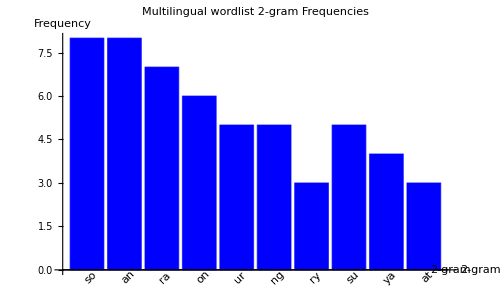

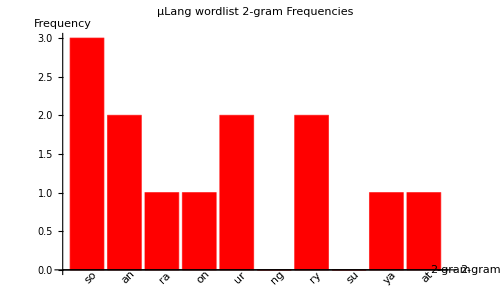

```mathematica
chart1=BarChart[#[[2]]&/@topData,ChartLabels->Placed[#[[1]]&/@topData,Below,Rotate[#,Pi/4]&],ChartStyle->Blue,PlotLabel->"Multilingual wordlist 2-gram Frequencies",AxesLabel->{"2-gram","Frequency"},ImageSize->500,AspectRatio->0.6]

chart2=BarChart[#[[3]]&/@topData,ChartLabels->Placed[#[[1]]&/@topData,Below,Rotate[#,Pi/4]&],ChartStyle->Red,PlotLabel->"μLang wordlist 2-gram Frequencies",AxesLabel->{"2-gram","Frequency"},ImageSize->500,AspectRatio->0.6]
```

```mathematica
stats=ngramStatistics[l1, l2,2];
"Statistical Summary (2-grams)\n" <>ToString[TableForm[{#,stats[#]}&/@Keys[stats],TableHeadings->{None,{"Metric","Value"}}]]

stats=ngramStatistics[l1, l2,3];
"Statistical Summary (3-grams)\n" <>ToString[TableForm[{#,stats[#]}&/@Keys[stats],TableHeadings->{None,{"Metric","Value"}}]]
```

Statistical Summary (2-grams)
   Metric                             Value
   TotalUniqueNgrams                  92

   MultilingualWordListUniqueNgrams   65

   μLangWordListUniqueNgrams          5

   SharedNgrams                       22

   JaccardSimilarity                  0.23913

Statistical Summary (3-grams)
   Metric                             Value
   TotalUniqueNgrams                  108

   MultilingualWordListUniqueNgrams   86

   μLangWordListUniqueNgrams          10

   SharedNgrams                       12

   JaccardSimilarity                  0.111111

## Ease of pronunciation

Considering the application of this work in actual conlanging, I also need to pick pronounceable words that can be spoken regularly. I heavily penalize consonant clusters longer than 4 consonants and also encourage a similar number of vowels and consonants. A greater score means a more difficult to pronounce word.

Implement a penalty for difficult to pronounce words:

```mathematica
pronounceabilityPenalty[str_String]:=Module[{syllables,vowelCount,consonantCount,vowelConsonantPenalty,rareClusterPenalty,totalScore},rareClusterPenalty=StringCount[str,RegularExpression["[^aeiouyAEIOUY]{3,}"]];
If[rareClusterPenalty>0,Return[1000]];
syllables=StringCount[ToLowerCase[str],RegularExpression["[aeiouy]+"]];
vowelCount=StringCount[str,RegularExpression["[aeiouyAEIOUY]"]];
consonantCount=StringLength[str]-vowelCount;
vowelConsonantPenalty=Abs[vowelCount-consonantCount]/StringLength[str];
totalScore=syllables+vowelConsonantPenalty;
totalScore
]
```

Sort generated average words by pronounceability:

```mathematica
pronounceabilityPenalty[#]&/@allPossibleWords;
sortedByPronunciation = SortBy[allPossibleWords,pronounceabilityPenalty];
sortedByPronunciation
```

{ria,qorr,sran,adla,ilan,kati,sourry,syne,sonaa,sourryya}

I think that if you extend this project on your own after the program, the method you use for pronounceability has room for improvement. Good starting idea though.

## Generating for the Swadesh Wordlist

The Swadesh Wordlist is a list of words for very common concepts, ideas, and objects. It is a staple in the conlanger’s toolkit as it gives inspiration for creating fundamental words for a lexicon. I combined all of my approaches into one large function and applied it on 10 random words from the Swadesh Wordlist.

```mathematica
GenerateLexicon[keyWord_String]:=Module[{languages,rawTranslations,translatedList,charLists,avgLen,augmentedLists,transposed,mostFreqChar,mostFreqCharWord,SYLLABLECOUNT,positionedDigrams,groupedByPosition,countsByPosition,topDigramsByPosition,generateWord,mostDigramGenerated,populationSize,generations,mutationRate,fitnessFunction,population,randomString,allBest,words,charSet,MAXLENGTH,allPopulations,avgFitnessPerGen,phoneticDifference,bestCandidate,fitnesses,parents,baseWord,testList,padChar,baseWordStates,targetWords,GENERATIONS,averageLength,allPossibleChars,rawFrequencies,charFreqWeights,initialState,evolutionResults,finalWord,bestDistance,testPositions,positionDict,net,vocabulary,results,trainednet,generator,wordz,bestWordGeneticPool,bestWord,newAvgWords,netPhon,symbolMap,ipaList,convertedTrainList,vocabularyPhon,resultsPhon,trainednetPhon,generatorPhon,wordzPhon,newAvgWordsPhonetics,lengthVaryTwoPointCrossover,mutate,getAllChars,pad,mostDifferentWord,findDifferingIndices,layoutTestWords,calculateCharFrequencies,normalizeFrequencies,weightedRandomTarget,randomMutation,evolveTowardWeighted,evolutionStep},
languages=EntityClass["Language",{"TotalSpeakers"->TakeLargest[100]}]//EntityList;
rawTranslations=KeyValueMap[#1->First[#2]&,WordTranslation[keyWord,languages]];
translatedList=DeleteCases[DeleteDuplicates[ToLowerCase[Select[Transliterate[Values[rawTranslations]],StringMatchQ[#,CharacterRange["A","z"]..]&]]],"notavailable"];
charLists=Characters/@translatedList;
avgLen=Round[Mean[Length/@charLists]];
augmentedLists=Map[Function[chars,If[Length[chars]>avgLen,Take[chars,avgLen],PadRight[chars,avgLen,"-"]]],charLists];
transposed=Transpose[augmentedLists];
mostFreqChar=Map[If[DeleteCases[#,"-"]==={},"-",First@First@SortBy[Tally@DeleteCases[#,"-"],-Last[#]&]]&,transposed];
mostFreqCharWord=StringJoin[DeleteCases[mostFreqChar,"-"]];
SYLLABLECOUNT=Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]];
positionedDigrams=Flatten[Table[If[StringLength[word]>=pos+1,{pos,StringTake[word,{pos,pos+1}]},Nothing],{word,translatedList},{pos,StringLength[word]-1}],1];
groupedByPosition=GroupBy[positionedDigrams,First->Last];
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[1]],{pos,Sort@Keys[countsByPosition]}];
generateWord[]:=Module[{numSyllables,selectedLists,syllables},numSyllables=RandomInteger[{Max[1,SYLLABLECOUNT-2],Min[Length[topDigramsByPosition],SYLLABLECOUNT+2]}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]];
mostDigramGenerated=DeleteDuplicates[Table[generateWord[],{7}]];
populationSize=100;
generations=5;
mutationRate=0.2;
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}];
allBest={};
words=translatedList;
charSet=Flatten[topDigramsByPosition];
MAXLENGTH=Round[Mean[StringLength/@words]];
phoneticDifference[word1_String,word2_String]:=Module[{soundex1,soundex2},soundex1=ResourceFunction["Soundex"][word1];
soundex2=ResourceFunction["Soundex"][word2];
If[soundex1===soundex2,0,EditDistance[soundex1,soundex2]]];
fitnessFunction[candidate_String]:=Module[{maxEditDistance,maxPhoneticDistance,editScore,phoneticScore},maxEditDistance=Max[EditDistance[candidate,#]&/@words];
maxPhoneticDistance=Max[phoneticDifference[candidate,#]&/@words];
editScore=If[maxEditDistance>0,1-N[Mean[EditDistance[candidate,#]&/@words]/maxEditDistance],1];
phoneticScore=If[maxPhoneticDistance>0,1-N[Mean[phoneticDifference[candidate,#]&/@words]/maxPhoneticDistance],1];
0.5*editScore+0.5*phoneticScore];
randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT,SYLLABLECOUNT+2}]];
lengthVaryTwoPointCrossover[p1_,p2_]:=Module[{len1,len2,minLen,pt1,pt2,c1,c2,child},len1=StringLength[p1];
len2=StringLength[p2];
minLen=Min[len1,len2];
{pt1,pt2}=Sort@RandomSample[Range[minLen],2];
c1=Characters[p1];
c2=Characters[p2];
child=Join[Take[c1,pt1-1],Take[c2,{pt1,pt2}],Drop[c1,pt2]];
If[Length[child]>MAXLENGTH,child=Take[child,MAXLENGTH]];
StringJoin[child]];
mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];
population=Table[randomString[],{populationSize}];
allBest=Table[fitnesses=fitnessFunction/@population;
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
population=Table[mutate@lengthVaryTwoPointCrossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];
bestCandidate,{gen,1,generations}];
bestWordGeneticPool=First@MaximalBy[allBest,fitnessFunction];
baseWord=StringJoin@RandomChoice[CharacterRange["a","z"],5];
testList=translatedList;
padChar="_";
GENERATIONS=1000;
getAllChars[wordList_]:=Module[{maxLen,paddedWords,allChars},maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
allChars=Union[Flatten[Characters/@paddedWords]];
allChars];
pad[w1_,w2_]:=Module[{maxLen,p1,p2},maxLen=Max[StringLength[w1],StringLength[w2]];
{StringPadRight[w1,maxLen,padChar],StringPadRight[w2,maxLen,padChar]}];
findDifferingIndices[str1_,str2_]:=Module[{minLen,diffs},minLen=Min[StringLength[str1],StringLength[str2]];
diffs=Select[Range[minLen],StringTake[str1,{#}]=!=StringTake[str2,{#}]&];
diffs];
calculateCharFrequencies[wordList_]:=Module[{maxLen,paddedWords,freqTables},maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
freqTables=Table[Counts[StringTake[#,{pos}]&/@paddedWords],{pos,1,maxLen}];
freqTables];
normalizeFrequencies[freqTable_]:=Module[{nonZeroEntries,total},nonZeroEntries=Select[freqTable,#>0&];
total=Total[Values[nonZeroEntries]];
If[total==0,freqTable,Association[#->If[freqTable[#]>0,N[freqTable[#]/total],0]&/@Keys[freqTable]]]];
weightedRandomTarget[base_,list_]:=Module[{diffs,total,weights},diffs=Table[{word,EditDistance[base,word]},{word,list}];
total=Total[diffs[[All,2]]];
If[total==0,RandomChoice[list],weights=(diffs[[All,2]]^3)/Total[diffs[[All,2]]^3];
RandomChoice[weights->diffs[[All,1]]]]];
evolveTowardWeighted[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i,targetChar,baseChar,weight,chars,weights,choice},{basePadded,targetPadded}=pad[base,target];
diffIndices=findDifferingIndices[basePadded,targetPadded];
If[diffIndices==={},basePadded,i=RandomChoice[diffIndices];
targetChar=StringTake[targetPadded,{i,i}];
baseChar=StringTake[basePadded,{i,i}];
weight=If[i<=Length[charFreqWeights],chars=Keys[charFreqWeights[[i]]];
weights=Values[charFreqWeights[[i]]];
choice=RandomChoice[weights->chars];
StringReplacePart[basePadded,choice,{i,i}],basePadded]]];
evolutionStep[{currentWord_,currentBest_,bestDist_,targetHist_,stateHist_}]:=Module[{target,newWord,newDist},target=weightedRandomTarget[currentWord,testList];
newWord=StringReplace[evolveTowardWeighted[currentWord,target],"_"->""];
newDist=Mean[EditDistance[newWord,#]&/@testList];
If[newDist<bestDist,{newWord,newWord,newDist,Append[targetHist,target],Append[stateHist,newWord]},{newWord,currentBest,bestDist,Append[targetHist,target],Append[stateHist,newWord]}]];

pronounceabilityScore[str_String]:=Module[{knownWords,syllables,vowelCount,consonantCount,vowelConsonantPenalty,dictionaryMatch,rareClusterPenalty,normalizedLength,totalScore},rareClusterPenalty=StringCount[str,RegularExpression["[^aeiouyAEIOUY]{3,}"]];
If[rareClusterPenalty>0,Return[1000]];
knownWords=DictionaryLookup["*"];
syllables=StringCount[ToLowerCase[str],RegularExpression["[aeiouy]+"]];
dictionaryMatch=Min[EditDistance[ToLowerCase[str],#]&/@Select[knownWords,Abs[StringLength[#]-StringLength[str]]<=2&]];
normalizedLength=StringLength[str]/10.0;
vowelCount=StringCount[str,RegularExpression["[aeiouyAEIOUY]"]];
consonantCount=StringLength[str]-vowelCount;
vowelConsonantPenalty=Abs[vowelCount-consonantCount]/StringLength[str];
totalScore=syllables+dictionaryMatch/10+vowelConsonantPenalty+normalizedLength;
totalScore;
];

allPossibleChars=getAllChars[testList];
rawFrequencies=calculateCharFrequencies[testList];
charFreqWeights=Map[normalizeFrequencies[AssociationThread[allPossibleChars,Lookup[#,allPossibleChars,0]]]&,rawFrequencies];
initialState={baseWord,baseWord,Mean[EditDistance[baseWord,#]&/@testList],{},{baseWord}};
evolutionResults=NestList[evolutionStep,initialState,GENERATIONS];
{finalWord,bestWord,bestDistance,targetWords,baseWordStates}=Last[evolutionResults];
bestWord=StringReplace[bestWord,"_"->""];
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"];
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]];
results=NetTrain[net,<|"Input"->translatedList|>,All,LossFunction->"Loss",MaxTrainingRounds->500];
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}];
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
newAvgWords=Sort@Complement[Table[wordz[],15],translatedList];


Module[{maxWords,paddedLists,tableData},maxWords=Max[1,Length[mostDigramGenerated],1,1,Length[newAvgWords],Length[newAvgWordsPhonetics]];
paddedLists={PadRight[{keyWord},maxWords,""],PadRight[{mostFreqCharWord},maxWords,""],PadRight[Reverse[SortBy[mostDigramGenerated,pronounceabilityScore]],maxWords,""],PadRight[{bestWordGeneticPool},maxWords,""],PadRight[{bestWord},maxWords,""],PadRight[Reverse[SortBy[newAvgWords,pronounceabilityScore]],maxWords,""](*,PadRight[newAvgWordsPhonetics,maxWords,""]*)};
tableData=Transpose[paddedLists];
TableForm[tableData,TableHeadings->{None,{"Original Keyword","Most Freq Char","Digram-Based","Genetic Algorithm","Evolution Algorithm","Neural Network"(*,"Neural Network Phonetic"*)}},TableAlignments->Center,TableSpacing->{2,1}]]]
```

Consider iconizing  much of the code; the reader would probably not be interested in long lists of local variable names, for instance. Also, your published paper should not contain code comments unless there is a strong reason for it.

```mathematica
ResourceObject["Swadesh Lists"]
```

ResourceObject[…]

```mathematica
swadeshData=ResourceData["Swadesh Lists"];
```

```mathematica
englishWords=Normal[Union[Flatten[Keys/@Values[swadeshData]]]];
```

```mathematica
GenerateLexicon[#]&/@ RandomSample[englishWords, 5]
```

{Original Keyword | Most Freq Char | Digram-Based | Genetic Algorithm | Evolution Algorithm | Neural Network
walk | naraaaa | caanhaalla | nakdta | naana | yuruy
 |  | caanhaal |  |  | perja
 |  | caan |  |  | pagba
 |  | ca |  |  | ngami
 |  |  |  |  | nadet
 |  |  |  |  | nadak
 |  |  |  |  | march,Original Keyword | Most Freq Char | Digram-Based | Genetic Algorithm | Evolution Algorithm | Neural Network
eye | aakh | anan | ioka | anh | jich
 |  | an |  |  | amkh
 |  | anankhha |  |  | ,Original Keyword | Most Freq Char | Digram-Based | Genetic Algorithm | Evolution Algorithm | Neural Network
tongue | linga | lion | lahn | lina | ulim
 |  | li |  |  | limb
 |  | lionnggu |  |  | lida
 |  | lionng |  |  | leta
 |  |  |  |  | leng
 |  |  |  |  | jaba
 |  |  |  |  | awny,Original Keyword | Most Freq Char | Digram-Based | Genetic Algorithm | Evolution Algorithm | Neural Network
bite | kataa | kaat | piica | pata | tutt
 |  | ka |  |  | stic
 |  | kaatnssa |  |  | pica
 |  | kaatns |  |  | musc
 |  |  |  |  | isir
 |  |  |  |  | gigi
 |  |  |  |  | gege
 |  |  |  |  | dans
 |  |  |  |  | cako,Original Keyword | Most Freq Char | Digram-Based | Genetic Algorithm | Evolution Algorithm | Neural Network
eye | aakh | an | iokh | ao | mua
 |  | anankhha |  |  | 
 |  | anankh |  |  | }

## Conclusion

This work introduces several methods to computationally generate “average” words that contain morphological and phonetic features of many different multilingual translations. I tried using the most frequent character, most frequent digram, a genetic algorithm, a string evolution algorithm and two autoregressive neural networks.

## Future Directions

The lexicon is just a small part of a full-fledged conlang. To ensure that μLang can operate as a truly speakable language, I need to decide on grammar rules such as word order, verb tenses, morphosyntactic alignment, and much more. I plan to use my work to develop a fully speakable conlang over this summer.

I hope you do. You have come up with some awesome approaches to new language development. This is a very well thought out and imaginative exploration of the subject. Bravo! I thoroughly enjoyed reading your paper.

## References

Kawasaki, H. (n.d.). An Acoustical Basis for Universal Constraints on Sound Sequences.
Soundex Algorithm—An overview | ScienceDirect Topics. (n.d.). Retrieved July 9, 2025, from https://www.sciencedirect.com/topics/computer-science/soundex-algorithm
WordPhoneticSyllabify | Wolfram Function Repository. (n.d.). Retrieved July 9, 2025, from https://resources.wolframcloud.com/FunctionRepository/resources/WordPhoneticSyllabify/
WordSyllables | Wolfram Function Repository. (n.d.). Retrieved July 9, 2025, from https://resources.wolframcloud.com/FunctionRepository/resources/WordSyllables/

## Acknowledgements

This project would not have been possible with the help of my mentor Mark Greenberg, my mentor group peers Adit Amit Kumar, Daniel Xu, and Viola Pande. I would also like to thank other mentors including Lyman Hurd, Anton Antonov, and Aayush Dubey. The directors of the Wolfram Summer Research Program, Rory Foulger, Eryn Gillam, and Megan Davis also played a key role in helping me formulate my ideas and publish my work.